```mathematica
$Assumptions = {Δ ∈ Reals, Δ < 0, q ∈ Reals, θ ∈ Reals, t ∈ Reals,t>=0, ϕ ∈ Reals,q>=0,γ∈Reals}
```

{Δ∈ℝ,Δ<0,q∈ℝ,θ∈ℝ,t∈ℝ,t≥0,ϕ∈ℝ,q≥0,γ∈ℝ}

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
H0 = FullSimplify[{{0, α * q * Cos[θ + 2 π/3], Conjugate[α] * q * Cos[θ + 4 π/3]}, {Conjugate[α] * q * Cos[θ + 2 π/3], 0, α * q * Cos[θ]}, {α * q * Cos[θ + 4 π/3], Conjugate[α] * q * Cos[θ], 0}}]
```

{{0,-q α Sin[π/6+θ],-q Conjugate[α] Sin[π/6-θ]},{-q Conjugate[α] Sin[π/6+θ],0,q α Cos[θ]},{-q α Sin[π/6-θ],q Conjugate[α] Cos[θ],0}}

```mathematica
M = {{0, Δ, Δ}, {Δ, 0, Δ}, {Δ, Δ, 0}}
```

{{0,Δ,Δ},{Δ,0,Δ},{Δ,Δ,0}}

```mathematica
H = FullSimplify[H0 + M]
```

{{0,Δ-q α Sin[π/6+θ],Δ-q Conjugate[α] Sin[π/6-θ]},{Δ-q Conjugate[α] Sin[π/6+θ],0,Δ+q α Cos[θ]},{Δ-q α Sin[π/6-θ],Δ+q Conjugate[α] Cos[θ],0}}

```mathematica
a = 0
d = Δ + Conjugate[α]*q*Cos[θ +2 π/3]
f =  Δ + α*q*Cos[θ+4 π/3]
b=0
e=  Δ + Conjugate[α]*q*Cos[θ]
c=0
```

0

Δ-ⅇ^(-ⅈ Conjugate[γ]) q Conjugate[t] Sin[π/6+θ]

Δ-ⅇ^(ⅈ γ) q t Sin[π/6-θ]

0

Δ+ⅇ^(-ⅈ Conjugate[γ]) q Conjugate[t] Cos[θ]

0

```mathematica
Clear[t, Δ, q, γ]
```

```mathematica
x1 = FullSimplify[ComplexExpand[a^2+b^2+c^2-a*b - a * c - b * c + 3 * (Abs[d]^2+Abs[f]^2+Abs[e]^2),α]]
```

(9 q^2 t^2)/2+9 Δ^2

```mathematica
x2 = FullSimplify[ComplexExpand[-(2*a-b-c)(2*b-a-c)(2*c-a-b)+9*((2*c-a-b)*Abs[d]^2+(2*b-a-c)*Abs[f]^2+(2*a-b-c)*Abs[e]^2)-54*Re[Conjugate[d]*Conjugate[e]*f],α]]
```

-27/2 (4 Δ^3+q^2 t^2 (-3 Δ Cos[2 γ]+q t Cos[3 γ] Cos[3 θ]))

```mathematica
α=t*Exp[I*γ]
```

ⅇ^(ⅈ γ) t

```mathematica
ϕ = FullSimplify[ComplexExpand[ArcTan[Sqrt[4(x1)^3-(x2)^2]/x2]]]
```

$Aborted

```mathematica
ϕ=π/2
```

π/2

```mathematica
q = 1
t = 1
γ=π/4
```

1

1

π/4

```mathematica
Clear[q, t, α, Δ, θ, γ]
```

```mathematica
FullSimplify[λ1]
```

FullSimplify::fas: Warning: one or more assumptions evaluated to False.

-√2

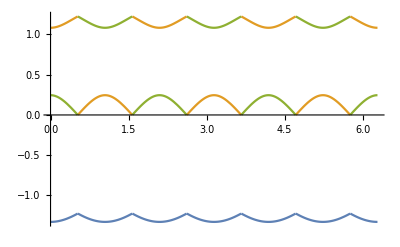

```mathematica
Plot[{λ1,λ2, λ3}, {θ, 0, 2*π}]
```

```mathematica
λ1=FullSimplify[ComplexExpand[1/3(a+b+c-2Sqrt[x1]*Cos[ϕ/3]),α]]
```

-√2 q t Cos[1/6 (Arg[1-ⅈ √(2-Cos[3 γ]^2 Cos[3 θ]^2) Sec[3 γ] Sec[3 θ]]-Arg[1+ⅈ √(2-Cos[3 γ]^2 Cos[3 θ]^2) Sec[3 γ] Sec[3 θ]])]

```mathematica
λ2=FullSimplify[ComplexExpand[1/3(a+b+c+2Sqrt[x1]*Cos[(ϕ-π)/3]),α]]
```

√2 q t Sin[1/6 (π+Arg[1-ⅈ √(2-Cos[3 γ]^2 Cos[3 θ]^2) Sec[3 γ] Sec[3 θ]]-Arg[1+ⅈ √(2-Cos[3 γ]^2 Cos[3 θ]^2) Sec[3 γ] Sec[3 θ]])]

```mathematica
λ3=FullSimplify[ComplexExpand[1/3(a+b+c+2Sqrt[x1]*Cos[(ϕ+π)/3]),α]]
```

√2 q t Sin[1/6 (π-Arg[1-ⅈ √(2-Cos[3 γ]^2 Cos[3 θ]^2) Sec[3 γ] Sec[3 θ]]+Arg[1+ⅈ √(2-Cos[3 γ]^2 Cos[3 θ]^2) Sec[3 γ] Sec[3 θ]])]

```mathematica
m1 = FullSimplify[Normal[Series[ComplexExpand[(d*(c-λ1)-Conjugate[e]*f)/(f*(b-λ1)-d*e),α],{q,0,2}]]]
```

(ⅇ^(-2 ⅈ γ) (3-2 √6 ⅇ^(3 ⅈ γ) Cos[θ] (-2+Cos[2 θ])-6 Cos[2 θ]-2 ⅇ^(6 ⅈ γ) Cos[θ] Cos[3 θ]))/(2 √6 Cos[3 γ] Cos[3 θ]+(-2+Cos[2 θ]) (4+Cos[2 θ]-√3 Sin[2 θ]))

```mathematica
m2 = FullSimplify[Normal[Series[ComplexExpand[(d*(c-λ2)-Conjugate[e]*f)/(f*(b-λ2)-d*e),α],{q,0,2}]]]
```

(Cos[2 γ] (3-6 Cos[2 θ])-2 ⅇ^(4 ⅈ γ) Cos[θ] Cos[3 θ]+√6 Cos[γ] (-3 Cos[θ]+Cos[3 θ])+2 ⅈ √6 Cos[θ] (-2+Cos[2 θ]) Sin[γ]+3 ⅈ (-1+2 Cos[2 θ]) Sin[2 γ])/(-2 √6 Cos[3 γ] Cos[3 θ]+(-2+Cos[2 θ]) (4+Cos[2 θ]-√3 Sin[2 θ]))

```mathematica
m3 = FullSimplify[Normal[Series[ComplexExpand[(d*(c-λ3)-Conjugate[e]*f)/(f*(b-λ3)-d*e),α],{q,0,2}]]]
```

1/4 ⅇ^(4 ⅈ γ) (-1+2 Cos[2 θ]) Csc[π/6+θ]^2

```mathematica
v1 =FullSimplify[Normal[Series[ComplexExpand[ {1/f(λ1-c-e*m1),m1,1},α],{q,0,2}]]]
```

{-((ⅇ^(-ⅈ (γ+5 θ)) (1-4 ⅇ^(2 ⅈ θ)+ⅇ^(4 ⅈ θ)) Csc[π/6-θ] (2 ⅇ^(3 ⅈ γ)+√6 ⅇ^(ⅈ θ)+√6 ⅇ^(5 ⅈ θ)+2 ⅇ^(3 ⅈ (γ+2 θ))-4 √2 ⅇ^(3 ⅈ θ) (√3-3 Cos[θ] Sin[θ])))/(8 (2 √6 Cos[3 γ] Cos[3 θ]+(-2+Cos[2 θ]) (4+Cos[2 θ]-√3 Sin[2 θ])))),-(2 ⅇ^(-2 ⅈ γ) (-3+6 Cos[2 θ]+2 ⅇ^(3 ⅈ γ) Cos[θ] (√6 (-2+Cos[2 θ])+ⅇ^(3 ⅈ γ) Cos[3 θ])))/(4 √6 Cos[3 γ] Cos[3 θ]+2 (-2+Cos[2 θ]) (4+Cos[2 θ]-√3 Sin[2 θ])),1}

```mathematica
v2 =FullSimplify[Normal[Series[ComplexExpand[ {1/f(λ1-c-e*m2),m2,1},α],{q,0,2}]]]
```

{-((ⅇ^(-ⅈ γ) Csc[π/6-θ] (2 Cos[3 γ] (Cos[θ]+20 Cos[3 θ]+Cos[5 θ])+2 ⅈ (Cos[θ]-4 Cos[3 θ]+Cos[5 θ]) Sin[3 γ]+3 √2 (7 √3-√3 Cos[4 θ]-4 Sin[2 θ]+Sin[4 θ])))/(-8 √6 Cos[3 γ] Cos[3 θ]+4 (-2+Cos[2 θ]) (4+Cos[2 θ]-√3 Sin[2 θ]))),(Cos[2 γ] (3-6 Cos[2 θ])-2 ⅇ^(4 ⅈ γ) Cos[θ] Cos[3 θ]+√6 Cos[γ] (-3 Cos[θ]+Cos[3 θ])+2 ⅈ √6 Cos[θ] (-2+Cos[2 θ]) Sin[γ]+3 ⅈ (-1+2 Cos[2 θ]) Sin[2 γ])/(-2 √6 Cos[3 γ] Cos[3 θ]+(-2+Cos[2 θ]) (4+Cos[2 θ]-√3 Sin[2 θ])),1}

```mathematica
v3 =FullSimplify[Normal[Series[ComplexExpand[ {1/f(λ1-c-e*m3),m3,1},α],{q,0,2}]]]
```

{(ⅇ^(-ⅈ γ) (2 √6-√6 Cos[2 θ]+2 ⅇ^(3 ⅈ γ) Cos[3 θ]+3 √2 Sin[2 θ]))/((-1+2 Cos[2 θ]) (Cos[θ]+√3 Sin[θ])),1/4 ⅇ^(4 ⅈ γ) (-1+2 Cos[2 θ]) Csc[π/6+θ]^2,1}